## D’Alambert’s Formula and Fourier Series Nilay Bhatt PDE - MATH 455 Fall 2017 Final Project The wave equation is an important second-order linear hyperbolic partial differential equation for the description of waves—as they occur in classical physics—such as sound waves, light waves and water waves. It arises in fields like acoustics, electromagnetics, and fluid dynamics. Historically, the problem of a vibrating string such as that of a musical instrument was studied by Jean le Rond d’Alembert, Leonhard Euler, Daniel Bernoulli, and Joseph-Louis Lagrange. In 1746, d’Alembert discovered the one-dimensional wave equation, and within ten years Euler discovered the three-dimensional wave equation We consider the equation u_tt = c^2 u_xx where u = u(t,x) is defined on the set 0 | < | x | ≤ | 1 , -∞ < t < ∞. We can prove that all the solutions of the wave equation can be written in the form u(t,x) = p(x - ct) + q(x + ct), where p, and q, are arbitray C^2 functions. d’Alambert’s formula u(t,x) = (f(x-ct) + f(x + ct))/2 + 1/(2c)∫_(x-ct)^(x+ct) g(z)ⅆz provides the solution to the initial value problem u_tt = c^2 u_xx u(0,x) = f(x) u_t(0,x) = g(x) In the classical sense if f(x) ∈ Ck and g(x) ∈ Ck−1 then u(t, x) ∈ Ck. However, the waveforms F and G may also be generalized functions, such as the delta-function. In that case, the solution may be interpreted as an impulse that travels to the right or the left. The basic wave equation is a linear differential equation and so it will adhere to the superposition principle. This means that the net displacement caused by two or more waves is the sum of the displacements which would have been caused by each wave individually. In addition, the behavior of a wave can be analyzed by breaking up the wave into components, e.g. the Fourier transform breaks up a wave into sinusoidal components. The problem that we are solving has homogeneous d’Alambert conditions applied to it, meaning u(t,0) = u(t,1) and u(0,x) = f(x) = x^2-x u_tt = u_xx u_t(0,x) = g(x) = 0 u(t,0) = u(t,1) = 0 so,

```mathematica
f[x_] = x^2 - x;
```

```mathematica
c = 1
```

1

```mathematica
g[x_] = 0
```

0

```mathematica
G[t_,x_] = Integrate[g[z], {z, x-t, x + t}];
```

```mathematica
u[t_,x_] = (f[x-t] + f[x + t])/2 + 1/(2) G[t,x];
```

```mathematica
1/2 (-2 x+(-t+x)^2+(t+x)^2)
```

1/2 (-2 x+(-t+x)^2+(t+x)^2)

```mathematica
string[t_]:= Plot[u[t,x],{x,-1,1},PlotRange->{{0,1}, {-2,2}}];
```

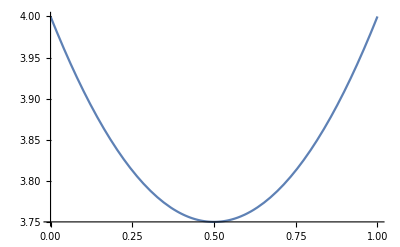

```mathematica
Plot[u[2,x],{x,0,1}]
```

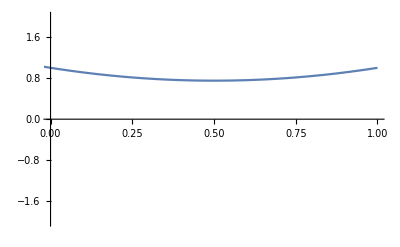

```mathematica
string[1]
```

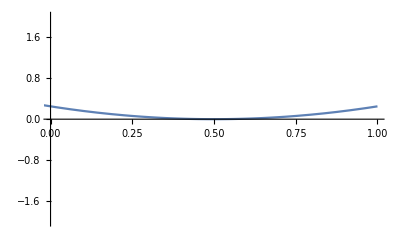

```mathematica
Show[string[0.5]]
```

```mathematica
Manipulate[Show[string[t]], {t,-1, 1}]
```

```mathematica
Plot3D[u[t,x], {t,0,3}, {x,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[u[t,x], {t,0,1}, {x,-1,1}, PlotRange-> {{0,1},{-1,1}, {-2,2}}, AxesOrigin -> {0,0,0}, Boxed -> False,Mesh->False]
```

-Graphics3D-

```mathematica
H[t_] = FourierTrigSeries[1/2 (-2 x+(-t+x)^2+(t+x)^2),t, 10]
```

π^2/3-x+x^2+4 (-Cos[t]+1/4 Cos[2 t]-1/9 Cos[3 t]+1/16 Cos[4 t]-1/25 Cos[5 t]+1/36 Cos[6 t]-1/49 Cos[7 t]+1/64 Cos[8 t]-1/81 Cos[9 t]+1/100 Cos[10 t])

```mathematica
Plot3D[π^2/3-x+x^2+4 (-Cos[t]+1/4 Cos[2 t]-1/9 Cos[3 t]+1/16 Cos[4 t]-1/25 Cos[5 t]+1/36 Cos[6 t]-1/49 Cos[7 t]+1/64 Cos[8 t]-1/81 Cos[9 t]+1/100 Cos[10 t]),{t,-0.5049635228713454,0.5050487360208393},{x,0.015694552990899946,1.0301109899424774}]
```

-Graphics3D-

```mathematica
H1[t_,n_] := FourierTrigSeries[1/2 (-2 x+(-t+x)^2+(t+x)^2),t, n]
```

```mathematica
H2[t_,n_] := FourierTrigSeries[1/2 (-10+(5-t)^2+(5+t)^2), t,n]
```

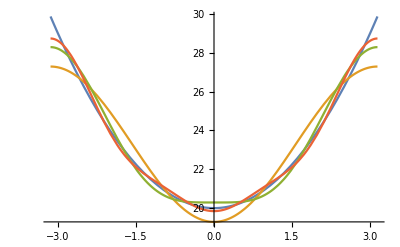

```mathematica
Plot[{1/2 (-10+(5-t)^2+(5+t)^2), Evaluate[H2[t,1]], Evaluate[H2[t,2]],  Evaluate[H2[t,3]]}, {t,-Pi,Pi} ]
```

```mathematica
u[t,  5]
```

1/2 (-10+(5-t)^2+(5+t)^2)